# Cálculo da matriz de impedância de um circuito de 138kV

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2024/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Library/CloudStorage/Dropbox/[07]Codes/[EEE457]_codes/arquivos_Mma_EEE457

```mathematica
<<LineCableParam2020`
```

```mathematica
dadoscond=Import["condcompleta.txt","Table"];
camp=Import["campos.txt","CSV"];
```

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
```

## Circuito 138kV -- 138CST1

Dados dos condutores -- código desenvolvido pelo Prof. Robson Dias
supondo que não há cabos pararraios no circuito

### Dados do condutor

```mathematica
Nome=ToUpperCase["dove"];
```

```mathematica
pos=Module[{posicao},posicao=If[NumberQ[Position[dadoscond,Nome][[1,1]]],Position[dadoscond,Nome][[1,1]],1];If[NumberQ[Position[dadoscond,Nome][[1,1]]],,Print["O condutor especificado não exite na tabela, verifique o nome digitado. Para não ocorrer erros nos cálculos foram utilizados os valores do condutor Owl"]];Return[posicao]];

{nome,MCM,NAl,DAl,NACO,DACO,secAl,secACO,Dcond,DALMA,PesoAl,PesoACO,Massa,CargaRupturaClasseA,CargaRupturaClasseB,Ampacidade,RMG,ResCC,ResAC,Xind,Xcap}=dadoscond[[pos]];

Table[Print[i,")  ",camp[[i,1]], " = ",dadoscond[[pos,i]]],{i,1,Length[camp]}];
```

Return[18]

1)  Nome comercial = DOVE

2)  Bitola (MCM) = 556.5

3)  Num. de Fios de Al. = 26

4)  Diâmetro dos Fios de Al. (mm) = 3.716

5)  Num. de Fios de Aço = 7

6)  Diâmetro dos Fios de Aço (mm) = 2.891

7)  Seção transversal de Al (mm^2) = 281.98

8)  Seção transversal do cond. (mm^2) = 327.9

9)  Diâmetro do cond. (mm) = 23.54

10)  Diâmetro da Alma de Aço (mm) = 8.67

11)  Peso Nominal do Al (aprox.) (kg/km) = 781.2

12)  Peso nominal do Aço (aprox.) (kg/km) = 358.9

13)  Massa (aprox.) (kg/km) = 1140.2

14)  Carga de ruptura (Classe A) (kgf) = 10274

15)  Carga de ruptura (Classe B) (kgf) = 9959

16)  Ampacidade (A) = 730

17)  Raio médio geométrico (m) = 0.0955

18)  Resistência elétrica máxima CC a 20.baC (Ohm/km) = 0.102

19)  Resistência elétrica máxima CA @ 60 Hz e 75.baC (Ohm/km) = 0.123

20)  Reatância indutiva (Ohm/km) = 0.3508

21)  Reatância capacitiva (Mohm/km) = 0.2121

### Dados condutores de fase (Dove)

```mathematica
r0=(dadoscond[[pos,10]]/2)*10^-3;   (* ⟹ [m] ⟸ *)
r1=(dadoscond[[pos,9]]/2)*10^-3;

ρAl=0.028264;    (* resistividade ⟹ Ω × mm^2/ m ⟸ *)
ρAlmetro=0.028264*10^-6;    (* ⟹ Ω × m ⟸ *)

Rdc=(dadoscond[[pos,19]])*10^-3;  (* ⟹ [Ω/m] ⟸⟹ @ 20^o ⟸*)

σϕ=(1/ρAlmetro)*(dadoscond[[pos,3]]*(dadoscond[[pos,4]]*10^-3/2)^2)/(r1^2-r0^2);
```

```mathematica
svao=0.35; (* comprimento do vão em [km] *)
T=dadoscond[[pos,15]];
W=dadoscond[[pos,13]];
H=0.24*T;
Ccat=H/W;
```

```mathematica
(*flecha em metro *)
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)
```

7.30891

## Visualiza Circuito

```mathematica
xc={3.4,-3.4,3.4};
yc=24.5-{3.8,3.8+1.9,3.8+3.8};
fl=flechacond{1, 1, 1};
yc= yc-2/3 fl; (* altura média *)
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,PlotRange->{{-5,5},{5,20.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## Cálculo das matrizes

faz parte do arquivo LineCableParam2020.wl

```mathematica
ω= 2. π 60;
ρs= 1000.;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc,yc,1/ρs, Rdc,r1,r0];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.182156+0.951535 ⅈ | 0.0586754+0.454439 ⅈ | 0.05871+0.501114 ⅈ
0.0586754+0.454439 ⅈ | 0.182225+0.951466 ⅈ | 0.0587442+0.454369 ⅈ
0.05871+0.501114 ⅈ | 0.0587442+0.454369 ⅈ | 0.182294+0.951396 ⅈ)

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+2.9082×10^-6 ⅈ | 0.-4.3034×10^-7 ⅈ | 0.-6.8463×10^-7 ⅈ
0.-4.3034×10^-7 ⅈ | 3.×10^-9+2.84688×10^-6 ⅈ | 0.-3.86153×10^-7 ⅈ
0.-6.8463×10^-7 ⅈ | 0.-3.86153×10^-7 ⅈ | 3.×10^-9+2.99793×10^-6 ⅈ)

### Cálculo da impedância de surto

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1, a^2, a},{1,a, a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Zseq=Diagonal[Inverse[A].Zmat.A];
Yseq=Diagonal[Inverse[A].Ymat.A];
```

Cálculo da impedância de surto para uma estimativa da potência do circuito

```mathematica
Zc=Sqrt[Im[Zseq]/Im[Yseq]][[2]]
```

375.323

```mathematica
Pn= (138 130)/Zc
```

47.7988

## Avaliação do desequilibrio do circuito

```mathematica
ℓ=80. 10^3; (* comprimento do circuito *)
```

Cálculo da impedância total do circuito:  impedância da linha curta + impedância da carga, aqui suposta igual a impedância de surto

```mathematica
Ztotal=Zmat ℓ + Re[Zc]DiagonalMatrix[{1,1,1}];
MatrixForm[Ztotal]
```

(389.896+76.1228 ⅈ | 4.69403+36.3551 ⅈ | 4.6968+40.0891 ⅈ
4.69403+36.3551 ⅈ | 389.901+76.1172 ⅈ | 4.69954+36.3495 ⅈ
4.6968+40.0891 ⅈ | 4.69954+36.3495 ⅈ | 389.907+76.1117 ⅈ)

```mathematica
aux=138 10^3/Sqrt[3]{1, a^2,a};
```

```mathematica
iabc=Inverse[Ztotal].aux
```

{206.362-20.5601 ⅈ,-120.785-166.735 ⅈ,-84.5941+185.779 ⅈ}

Para que o circuito fosse equilibrado seria necessário ter as três correntes com igual amplitude e defasadas de 120 graus

```mathematica
Abs[iabc]
```

{207.383,205.887,204.132}

```mathematica
ang1=Table[Arg[iabc[[i]]]/π 180 ,{i,3}]
```

{-5.68968,-125.92,114.482}

```mathematica
ang2=Arg[iabc[[1]]]/π 180  +{0, -120, 120}
```

{-5.68968,-125.69,114.31}

```mathematica
ang2-ang1
```

{0.,0.230388,-0.171776}

```mathematica
iabcsim= iabc[[1]] Exp[I {0, -120 Degree, 120 Degree}];
```

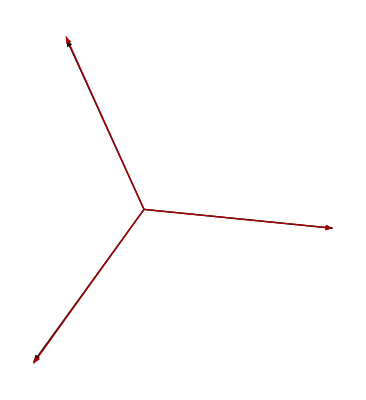

```mathematica
o1=Graphics[Table[Arrow[{{0,0},{Re[iabc[[i]]],Im[iabc[[i]]] }}],{i,3}]];
o2=Graphics[{Darker@Red,Table[Arrow[{{0,0},{Re[iabcsim[[i]]],Im[iabcsim[[i]]] }}],{i,3}]}];
Show[{o1,o2}]
```

cálculo da tensão na carga

```mathematica
Vr= Zc iabc
```

{77452.4-7716.68 ⅈ,-45333.4-62579.4 ⅈ,-31750.1+69727.1 ⅈ}

```mathematica
Abs[Vr] Sqrt[3]/(138 10^3)
```

{0.976925,0.969876,0.961608}

Cálculo dos componentes de sequência
Vabc = A V012

```mathematica
V012= Inverse[A] .Vr
```

{122.952-189.69 ⅈ,76858.3-7684.64 ⅈ,471.113+157.644 ⅈ}

```mathematica
Abs[V012]Sqrt[3]/( 138 10^3)
```

{0.0028372,0.969465,0.00623524}

Como se cálculo o nível de desequilibrio de um circuito?
Seq -/ Seq+  e Seq 0/Seq +

```mathematica
Abs[V012[[3]]/V012[[2]]]
```

0.00643163

```mathematica
Abs[V012[[1]]/V012[[2]]]
```

0.00292656

## Impacto dos cabos pararraios

### novas coordenadas dos condutores

```mathematica
xc={3.4,-3.4,3.4, -2.6, 2.6};
yc=24.5-{3.8,3.8+1.9,3.8+3.8,-2.8,-2.8};
fl=Join[flechacond{1, 1, 1}, .7 flechacond {1,1}];
yc= yc-2/3 fl;
```

```mathematica
yc
```

{15.8274,13.9274,12.0274,23.8892,23.8892}

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,PlotRange->{{-5,5},{5,25.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

### dados dos cabos pararraios

```mathematica
rpr= 4.57 10^-3;
rdcpr = 4.19 10^-3;
npr =2;
```

```mathematica
{Zm1, Ym1} =cZYlt[ω,xc,yc,1/ρs, Rdc,r1,r0, npr, rdcpr, rpr];
```

```mathematica
MatrixForm[Zm1 1000]
```

(0.227361+0.897649 ⅈ | 0.102247+0.402017 ⅈ | 0.100936+0.449925 ⅈ
0.102247+0.402017 ⅈ | 0.224288+0.900438 ⅈ | 0.099458+0.404567 ⅈ
0.100936+0.449925 ⅈ | 0.099458+0.404567 ⅈ | 0.221735+0.902774 ⅈ)

```mathematica
MatrixForm[(Zmat-Zm1) 1000]
```

(-0.0452044+0.0538865 ⅈ | -0.0435718+0.0524214 ⅈ | -0.0422257+0.0511884 ⅈ
-0.0435718+0.0524214 ⅈ | -0.0420631+0.051028 ⅈ | -0.0407138+0.0498023 ⅈ
-0.0422257+0.0511884 ⅈ | -0.0407138+0.0498023 ⅈ | -0.0394409+0.0486221 ⅈ)

```mathematica
Z012spr=1000Diagonal[Inverse[A].Zmat.A]
```

{0.299645+1.89141 ⅈ,0.123515+0.481492 ⅈ,0.123515+0.481492 ⅈ}

```mathematica
Z012=1000Diagonal[Inverse[A].Zm1.A]
```

{0.426222+1.73796 ⅈ,0.123581+0.48145 ⅈ,0.123581+0.48145 ⅈ}

```mathematica
Z012spr[[1]]
```

0.299645+1.89141 ⅈ

```mathematica
Z012[[1]]
```

0.426222+1.73796 ⅈ